### Start choosing the example:

```mathematica
t=9;
beta = 0;
A = 0.2;
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4},Adjacency Matrix→{{0,1,0,0},{0,0,0,1},{0,1,0,0},{0,0,0,0}},Entrance Vertices and Currents→{{1,I1},{3,I2}},Exit Vertices and Terminal Costs→{{4,U1}},Switching Costs→{}|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1->80,I2->30,U1->15}];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 0.006468 seconds to reduce with NewReduce!

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.022698,Null}

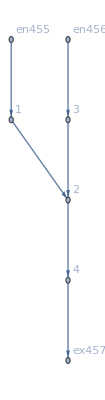

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j458→80.,j459→110.,j460→30.,j461→110.,j462→80.,j463→30.,j464→0.,j465→0.,j466→0.,j467→0.,j468→0.,j469→0.,jt470→0.,jt471→80.,jt472→80.,jt473→0.,jt474→0.,jt475→0.,jt476→0.,jt477→30.,jt478→0.,jt479→30.,jt480→110.,jt481→0.,u482→205.,u483→125.,u484→155.,u485→15.,u486→205.,u487→155.,u488→125.,u489→15.,u490→125.,u491→15.,u492→205.,u493→155.|>

#### Non-linear case

```mathematica
alpha = 0;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.98128×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.98128×10^-17

<|j458→80.,j459→110.,j460→30.,j461→110.,j462→80.,j463→30.,j464→0.,j465→0.,j466→0.,j467→0.,j468→0.,j469→0.,jt470→0.,jt471→80.,jt472→80.,jt473→0.,jt474→0.,jt475→0.,jt476→0.,jt477→30.,jt478→0.,jt479→30.,jt480→110.,jt481→0.,u482→20.2696,u483→17.6876,u484→19.9223,u485→15.,u486→20.2696,u487→19.9223,u488→17.6876,u489→15.,u490→17.6876,u491→15.,u492→20.2696,u493→19.9223|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.0483×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.0483×10^-17

<|j458→80.,j459→110.,j460→30.,j461→110.,j462→80.,j463→30.,j464→0.,j465→0.,j466→0.,j467→0.,j468→0.,j469→0.,jt470→0.,jt471→80.,jt472→80.,jt473→0.,jt474→0.,jt475→0.,jt476→0.,jt477→30.,jt478→0.,jt479→30.,jt480→110.,jt481→0.,u482→21.5012,u483→18.3398,u484→20.9562,u485→15.,u486→21.5012,u487→20.9562,u488→18.3398,u489→15.,u490→18.3398,u491→15.,u492→21.5012,u493→20.9562|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.33236×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.33236×10^-17

<|j458→80.,j459→110.,j460→30.,j461→110.,j462→80.,j463→30.,j464→0.,j465→0.,j466→0.,j467→0.,j468→0.,j469→0.,jt470→0.,jt471→80.,jt472→80.,jt473→0.,jt474→0.,jt475→0.,jt476→0.,jt477→30.,jt478→0.,jt479→30.,jt480→110.,jt481→0.,u482→25.5193,u483→20.4954,u484→24.2394,u485→15.,u486→25.5193,u487→24.2394,u488→20.4954,u489→15.,u490→20.4954,u491→15.,u492→25.5193,u493→24.2394|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.6479×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.6479×10^-17

<|j458→80.,j459→110.,j460→30.,j461→110.,j462→80.,j463→30.,j464→0.,j465→0.,j466→0.,j467→0.,j468→0.,j469→0.,jt470→0.,jt471→80.,jt472→80.,jt473→0.,jt474→0.,jt475→0.,jt476→0.,jt477→30.,jt478→0.,jt479→30.,jt480→110.,jt481→0.,u482→118.768,u483→73.8023,u484→93.399,u485→15.,u486→118.768,u487→93.399,u488→73.8023,u489→15.,u490→73.8023,u491→15.,u492→118.768,u493→93.399|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1.57004×10^-13,ComplexInfinity]

<|j458→80.,j459→110.,j460→30.,j461→110.,j462→80.,j463→30.,j464→0.,j465→0.,j466→0.,j467→0.,j468→0.,j469→0.,jt470→0.,jt471→80.,jt472→80.,jt473→0.,jt474→0.,jt475→0.,jt476→0.,jt477→30.,jt478→0.,jt479→30.,jt480→110.,jt481→0.,u482→205.,u483→125.,u484→155.,u485→15.,u486→205.,u487→155.,u488→125.,u489→15.,u490→125.,u491→15.,u492→205.,u493→155.|>

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.07055×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.07055×10^-16

<|j458→80.,j459→110.,j460→30.,j461→110.,j462→80.,j463→30.,j464→0.,j465→0.,j466→0.,j467→0.,j468→0.,j469→0.,jt470→0.,jt471→80.,jt472→80.,jt473→0.,jt474→0.,jt475→0.,jt476→0.,jt477→30.,jt478→0.,jt479→30.,jt480→110.,jt481→0.,u482→952.896,u483→588.99,u484→679.535,u485→15.,u486→952.896,u487→679.535,u488→588.99,u489→15.,u490→588.99,u491→15.,u492→952.896,u493→679.535|>

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.49007×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.49007×10^-17

<|j458→80.,j459→110.,j460→30.,j461→110.,j462→80.,j463→30.,j464→0.,j465→0.,j466→0.,j467→0.,j468→0.,j469→0.,jt470→0.,jt471→80.,jt472→80.,jt473→0.,jt474→0.,jt475→0.,jt476→0.,jt477→30.,jt478→0.,jt479→30.,jt480→110.,jt481→0.,u482→76975.9,u483→54135.4,u484→55829.9,u485→15.,u486→76975.9,u487→55829.9,u488→54135.4,u489→15.,u490→54135.4,u491→15.,u492→76975.9,u493→55829.9|>

```mathematica
alpha = 1.6;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.54095×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.54095×10^-17

<|j458→80.,j459→110.,j460→30.,j461→110.,j462→80.,j463→30.,j464→0.,j465→0.,j466→0.,j467→0.,j468→0.,j469→0.,jt470→0.,jt471→80.,jt472→80.,jt473→0.,jt474→0.,jt475→0.,jt476→0.,jt477→30.,jt478→0.,jt479→30.,jt480→110.,jt481→0.,u482→1.18884×10^6,u483→898799.,u484→908525.,u485→15.,u486→1.18884×10^6,u487→908525.,u488→898799.,u489→15.,u490→898799.,u491→15.,u492→1.18884×10^6,u493→908525.|>

```mathematica
alpha = 1.8;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.87912×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.87912×10^-17

<|j458→80.,j459→110.,j460→30.,j461→110.,j462→80.,j463→30.,j464→0.,j465→0.,j466→0.,j467→0.,j468→0.,j469→0.,jt470→0.,jt471→80.,jt472→80.,jt473→0.,jt474→0.,jt475→0.,jt476→0.,jt477→30.,jt478→0.,jt479→30.,jt480→110.,jt481→0.,u482→3.02767×10^11,u483→2.78714×10^11,u484→2.78731×10^11,u485→15.,u486→3.02767×10^11,u487→2.78731×10^11,u488→2.78714×10^11,u489→15.,u490→2.78714×10^11,u491→15.,u492→3.02767×10^11,u493→2.78731×10^11|>

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.48287×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.48287×10^-17

<|j458→80.,j459→110.,j460→30.,j461→110.,j462→80.,j463→30.,j464→0.,j465→0.,j466→0.,j467→0.,j468→0.,j469→0.,jt470→0.,jt471→80.,jt472→80.,jt473→0.,jt474→0.,jt475→0.,jt476→0.,jt477→30.,jt478→0.,jt479→30.,jt480→110.,jt481→0.,u482→8.5312×10^20,u483→8.47516×10^20,u484→8.47516×10^20,u485→15.,u486→8.5312×10^20,u487→8.47516×10^20,u488→8.47516×10^20,u489→15.,u490→8.47516×10^20,u491→15.,u492→8.5312×10^20,u493→8.47516×10^20|>

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.06128×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.06128×10^-16

<|j458→80.,j459→110.,j460→30.,j461→110.,j462→80.,j463→30.,j464→0.,j465→0.,j466→0.,j467→0.,j468→0.,j469→0.,jt470→0.,jt471→80.,jt472→80.,jt473→0.,jt474→0.,jt475→0.,jt476→0.,jt477→30.,jt478→0.,jt479→30.,jt480→110.,jt481→0.,u482→5.23663×10^106,u483→3.03173×10^106,u484→3.85857×10^106,u485→15.,u486→5.23663×10^106,u487→3.85857×10^106,u488→3.03173×10^106,u489→15.,u490→3.03173×10^106,u491→15.,u492→5.23663×10^106,u493→3.85857×10^106|>